#### Pár komentářů k Vašemu vypracování :

Pro lepší čitelnost je dobré oddělit jednotlivé části úlohy (například pomocí sekcí).

Řešení působí dost “pracovně” - například před integrálem máte na vstupu Indeterminate - asi nějaký pozůstatek z předchozí části úlohy. Ve 3. části úlohy máte prázdné buňky.

Ve třetí úloze byla chyba v zadání (vypadlo znaménko). Pokud byste měl úlohu naprogramovanou optimálně, tak by stačilo znaménko na jednom řádku opravit. Ve Vašem případě jste měl využít výsledků funkce Eigensystem nebo Eigenvalues, Eigenvectors. Upravil jsem Vám u 4. bodu úlohy. Stejně byste postupoval v případě 5. bodu úlohy.

Je dobré nemíchat stejná označení pro funkce a pro výrazy (H u třetí části úlohy, H[Δ,Ω] u poslední části úlohy). Doporučuji použít jen funkci H[Δ,Ω].

Mathematica nerozlišuje “sloupcové” a “řádkové” vektory. Proto lze ψ0 a ψ0dual lze reprezentovat stejným vektorem (kdyby byly vektory komplexní, musel byste duální vektor komplexně sdružit).

Celkově hodnotím 8 body.

## Limita

```mathematica
Limit[((Sin[x]+x^3)^(1/3)-x)/x^5,x-> 0]
```

Indeterminate

## Integrál

```mathematica
Indeterminate

Integrate[Log[x]/((x^2+1)^2),{x,0,∞}]
```

Indeterminate

-π/4

## Matice

```mathematica
H={{Δ,Ω},{Ω,-Δ}};
{eigenvalues,eigenvectors}=Eigensystem[H];


normalizedEigenvectors=Map[#/Norm[#]&,eigenvectors];


Print["Vlastné hodnoty: ",eigenvalues];
Print["Normalizované vlastné vektory:"];
Scan[Print[MatrixForm[#]]&,normalizedEigenvectors];
```

Vlastné hodnoty: {-√(Δ^2+Ω^2),√(Δ^2+Ω^2)}

Normalizované vlastné vektory:

(-(-Δ+√(Δ^2+Ω^2))/(Ω √(1+Abs[(-Δ+√(Δ^2+Ω^2))/Ω]^2))
1/(√(1+Abs[(-Δ+√(Δ^2+Ω^2))/Ω]^2)))

(-(-Δ-√(Δ^2+Ω^2))/(Ω √(1+Abs[(-Δ-√(Δ^2+Ω^2))/Ω]^2))
1/(√(1+Abs[(-Δ-√(Δ^2+Ω^2))/Ω]^2)))

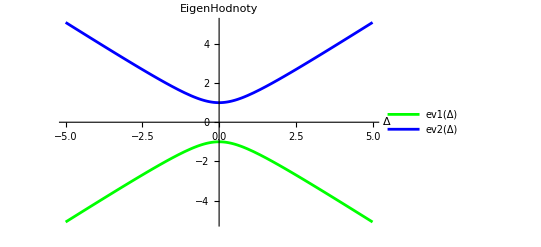

```mathematica
f[d_]:=eigenvalues[[1]]/.{Δ->d,Ω->1}
g[d_]:=eigenvalues[[2]]/.{Δ->d,Ω->1}

Plot[{f[Δ],g[Δ]},{Δ,-5,5},PlotStyle->{Green,Blue},AxesLabel->{"Δ","EigenHodnoty"},PlotLegends->{"ev1(Δ)","ev2(Δ)"}]
```

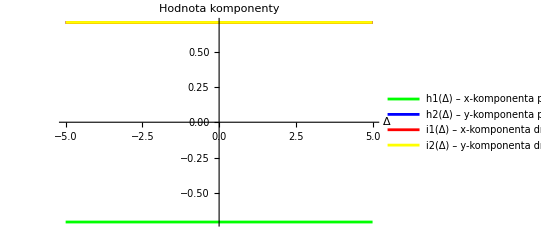

```mathematica
h1[Δ_]:=-1/Sqrt[2]
h2[Δ_]:=1/Sqrt[2]
i1[Δ_]:=1/Sqrt[2]
i2[Δ_]:=1/Sqrt[2]

Plot[{h1[Δ],h2[Δ],i1[Δ],i2[Δ]},{Δ,-5,5},PlotStyle->{Green,Blue,Red,Yellow},AxesLabel->{"Δ","Hodnota komponenty"},PlotLegends->{"h1(Δ) – x-komponenta prvého vlastného vektora","h2(Δ) – y-komponenta prvého vlastného vektora","i1(Δ) – x-komponenta druhého vlastného vektora","i2(Δ) – y-komponenta druhého vlastného vektora"}]
```

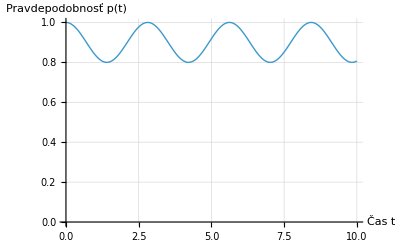

```mathematica
ψ0={1,0};

ψ0dual=ConjugateTranspose[ψ0];
H[Δ_,Ω_]:={{Δ,Ω},{Ω,-Δ}};
U[t_,Δ_,Ω_]:=MatrixExp[-I*H[Δ,Ω]*t];
ψ[t_,Δ_,Ω_]:=U[t,Δ,Ω].ψ0;
p[t_,Δ_,Ω_]:=Abs[ψ0dual.ψ[t,Δ,Ω]]^2;
Δvalue=1;
Ωvalue=0.5;


Plot[p[t,Δvalue,Ωvalue],{t,0,10},AxesLabel->{"Čas t","Pravdepodobnosť p(t)"},PlotRange->{0,1},GridLines->Automatic,PlotStyle->Thick]
```